```mathematica
x = {
(*noise*) 0.1,
(*ts*)1000,
(*M*)10^(k),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.000001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324
};
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];

growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]);
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
```

```mathematica
starvefn[y_]:=N[ts*-Bm/(Em*Log[1-f0*y^(γ-1)])]
```

```mathematica
recoveryfn[y_]:=N[ ts*- ((η-1)*Bm/Em)/(Log[1-(y*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (y*(1-f0*y^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]
```

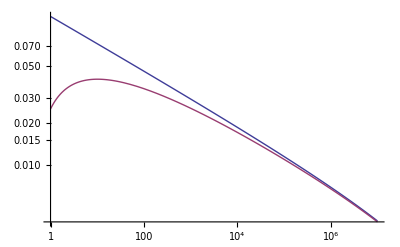

```mathematica
LogLogPlot[{starvefn[y],recoveryfn[y]},{y,1,10^7},PlotRange->All]
```

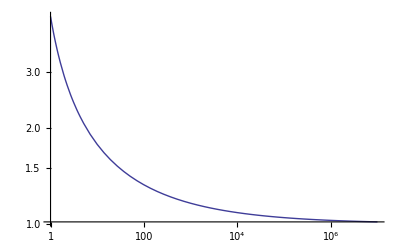

```mathematica
LogLogPlot[starvefn[y]/recoveryfn[y],{y,1,10^7},PlotRange->All]
```

```mathematica
Jac = ({{ts*(λ-(1-R) σ), ts*R ρ, ts*H ρ+F σ}, {ts*(1-R) σ, ts*(-μ-R ρ), ts*(-H ρ-F σ)}, {ts*(-m R), ts*(-R ρ), ts*(-F m+(1-R) α-R α-H ρ)}});
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
JacSpecSol = FullSimplify[Jac/.{R->Rstar, H->Hstar, F->Fstar}];
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,ρ];
```

$Aborted

```mathematica
plts={};
vals={};
Do[
x = {
(*noise*) 0.1,
(*ts*)1000,
(*M*)10^(k),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.000001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324
};
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];

growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]);
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+ RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*0.5*(1 + RandomReal[{-noise,noise}]);
tab=Table[{10^i,Abs[Select[Chop[ρ/.(HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth,σ->10^i})],#>0&][[1]]-recovery]},{i,-5,3,.015}];
plt=Show[{ListLogLogPlot[tab,Joined->True]},PlotRange->All];
plts=Append[plts,plt];
vals=Append[vals,{10^k,Sort[tab,#1[[2]]<#2[[2]]&][[1]][[1]]}]
,
{k,1,4,.25}]
```

Greater::nord: Invalid comparison with -0.0045671 + 0.0000756237\ ⅈ attempted.

Greater::nord: Invalid comparison with -0.0045671 - 0.0000756237\ ⅈ attempted.

Greater::nord: Invalid comparison with -0.00460062 + 0.000219864\ ⅈ attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

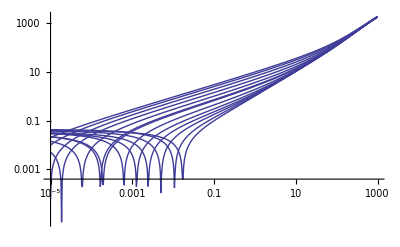

```mathematica
Show[plts]
```

```mathematica
vals
```

{{10.,0.017378},{17.7828,0.0107152},{31.6228,0.00501187},{56.2341,0.00242661},{100.,0.00125893},{177.828,0.000630957},{316.228,0.000194984},{562.341,0.000164059},{1000.,0.000060256},{1778.28,0.0000186209},{3162.28,0.00001},{5623.41,0.00001},{10000.,0.00001}}

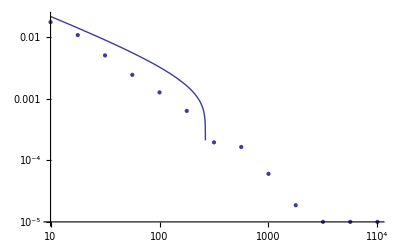

```mathematica
Show[{ListLogLogPlot[vals],LogLogPlot[N[ts*-Bm/(Em*Log[1-f0*M^(1.7-1)])],{M,10,10000}]},PlotRange->All]
```

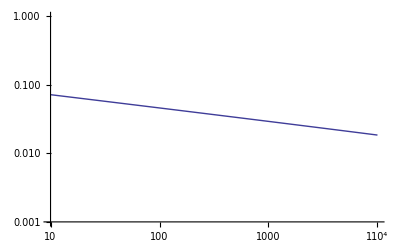

```mathematica
LogLogPlot[ N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])],{M,10,10000},PlotRange->{All,{.001,1}}]
```

#### Rest

```mathematica
x = {
(*noise*) 0.1,
(*ts*)1000,
(*M*)10^(7),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.000001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324
};
```

```mathematica
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
Jac = ({{ts*(λ-(1-R) σ), ts*R ρ, ts*H ρ+F σ}, {ts*(1-R) σ, ts*(-μ-R ρ), ts*(-H ρ-F σ)}, {ts*(-m R), ts*(-R ρ), ts*(-F m+(1-R) α-R α-H ρ)}});
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
```

```mathematica
JacSpecSol = FullSimplify[Jac/.{R->Rstar, H->Hstar, F->Fstar}];
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,ρ];
```

```mathematica
growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]);
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+ RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*0.5*(1 + RandomReal[{-noise,noise}]);
(*Replace everything except rho and sigma to build the curve*)
(*HopfSol = HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth};*)
sigvalues = RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==0.0000001},sig,{n,1,80}];
```

```mathematica
sigvalues
```

{1.×10^-7,1.5×10^-7,2.25×10^-7,3.375×10^-7,5.0625×10^-7,7.59375×10^-7,1.13906×10^-6,1.70859×10^-6,2.56289×10^-6,3.84434×10^-6,5.7665×10^-6,8.64976×10^-6,0.0000129746,0.000019462,0.0000291929,0.0000437894,0.0000656841,0.0000985261,0.000147789,0.000221684,0.000332526,0.000498789,0.000748183,0.00112227,0.00168341,0.00252512,0.00378768,0.00568151,0.00852227,0.0127834,0.0191751,0.0287627,0.043144,0.064716,0.097074,0.145611,0.218416,0.327625,0.491437,0.737155,1.10573,1.6586,2.4879,3.73185,5.59777,8.39666,12.595,18.8925,28.3387,42.5081,63.7622,95.6432,143.465,215.197,322.796,484.194,726.291,1089.44,1634.15,2451.23,3676.85,5515.27,8272.91,12409.4,18614.,27921.1,41881.6,62822.4,94233.6,141350.,212026.,318038.,477057.,715586.,1.07338×10^6,1.61007×10^6,2.4151×10^6,3.62265×10^6,5.43398×10^6,8.15097×10^6}

```mathematica
{starvation,recovery}
```

{0.00426695,0.00427952+0. ⅈ}

```mathematica
ρ/.(HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth,σ->.1})[[1]][[1]]
```

-519.547+2.78164×10^-22 ⅈ

Greater::nord: Invalid comparison with -484.604 - 16.9373\ ⅈ attempted.

Greater::nord: Invalid comparison with -484.604 + 16.9373\ ⅈ attempted.

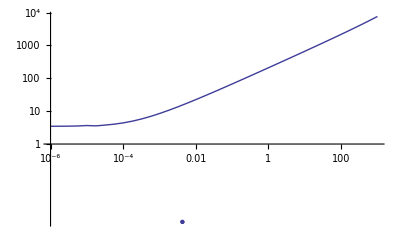

```mathematica
tab=Table[{10^i,Select[Chop[ρ/.(HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth,σ->10^i})],#>0&][[1]]},{i,-6,3,.25}];
Show[{ListLogLogPlot[tab,Joined->True],ListLogLogPlot[{Re[{starvation,recovery}]}]},PlotRange->All]
```

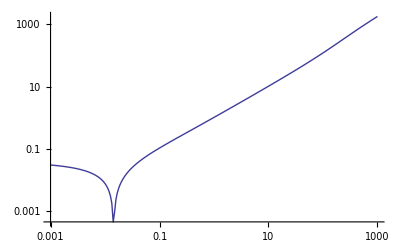

```mathematica
tab=Table[{10^i,Abs[Select[Chop[ρ/.(HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth,σ->10^i})],#>0&][[1]]-recovery]},{i,-3,3,.025}];
Show[{ListLogLogPlot[tab,Joined->True]},PlotRange->All]
```

```mathematica
Sort[tab,#1[[2]]<#2[[2]]&][[1]]
```

{0.0141254,0.000461836}

```mathematica
Show[{ListLogLogPlot[tab,Joined->True],ListLogLogPlot[{Re[{starvation,recovery}]}]},PlotRange->All]
```

```mathematica
NMinimize[Abs[Chop[ρ/.(HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth,σ->10^i})],#>0&][[1]]-recovery]
```

```mathematica
starvation
recovery
```

0.0316436

0.0229656+0. ⅈ

```mathematica
hopf1=ρ/.(HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth})[[1]][[1]];
```

```mathematica
NMinimize[hopf1==recovery,σ]
```

$Aborted

```mathematica
starvation
```

0.0316436

```mathematica
recovery
```

0.0229656+0. ⅈ

```mathematica
HopfSol = ParallelTable[{sig,N[ρ/.(HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth,σ->sig})]},{sig,sigvalues}]
```

{{1.×10^-7,{-0.000874816-0.00436732 ⅈ,-0.000874816+0.00436732 ⅈ,0.00148714,454555.}},{1.5×10^-7,{-0.00100237-0.00276214 ⅈ,-0.00100237+0.00276214 ⅈ,0.00174229,302863.}},{2.25×10^-7,{-0.00115282-0.00195313 ⅈ,-0.00115282+0.00195313 ⅈ,0.00204328,201735.}},{3.375×10^-7,{-0.0013308-0.00169146 ⅈ,-0.0013308+0.00169146 ⅈ,0.00239934,134317.}},{5.0625×10^-7,{-0.00154194-0.00169146 ⅈ,-0.00154194+0.00169146 ⅈ,0.00282179,89371.2}},{7.59375×10^-7,{-0.0017932-0.00182698 ⅈ,-0.0017932+0.00182698 ⅈ,0.00332456,59407.5}},{1.13906×10^-6,{-0.00209312-0.00193781 ⅈ,-0.00209312+0.00193781 ⅈ,0.00392478,39431.6}},{1.70859×10^-6,{-0.00245223-0.00205717 ⅈ,-0.00245223+0.00205717 ⅈ,0.00464357,26114.4}},{2.56289×10^-6,{-0.0028835-0.002151 ⅈ,-0.0028835+0.002151 ⅈ,0.00550698,17236.2}},{3.84434×10^-6,{-0.00340294-0.00217597 ⅈ,-0.00340294+0.00217597 ⅈ,0.00654714,11317.4}},{5.7665×10^-6,{-0.00403024-0.00206778 ⅈ,-0.00403024+0.00206778 ⅈ,0.00780366,7371.59}},{8.64976×10^-6,{-0.00478964-0.0016775 ⅈ,-0.00478964+0.0016775 ⅈ,0.00932535,4741.03}},{0.0000129746,{-0.00632131+3.76523×10^-17 ⅈ,-0.00510061-4.04768×10^-17 ⅈ,0.0111723+2.82448×10^-18 ⅈ,2987.32-9.0099×10^-29 ⅈ}},{0.000019462,{-0.00935894+1.02722×10^-17 ⅈ,-0.00430266-1.32032×10^-17 ⅈ,0.0134185+2.93095×10^-18 ⅈ,1818.18-3.57872×10^-28 ⅈ}},{0.0000291929,{-0.0123137+1.25952×10^-17 ⅈ,-0.00407444-1.77253×10^-17 ⅈ,0.0161548+5.13009×10^-18 ⅈ,1038.75-2.73802×10^-27 ⅈ}},{0.0000437894,{-0.0157521+3.40198×10^-17 ⅈ,-0.00395947-5.11273×10^-17 ⅈ,0.0194929+1.71075×10^-17 ⅈ,519.136-5.24675×10^-26 ⅈ}},{0.0000656841,{-0.0198733+2.31859×10^-17 ⅈ,-0.00389332-3.66805×10^-17 ⅈ,0.0235699+1.34945×10^-17 ⅈ,172.724-5.39592×10^-25 ⅈ}},{0.0000985261,{-58.2169+2.08138×10^-23 ⅈ,-0.0248642-6.2879×10^-17 ⅈ,-0.00385288+1.03612×10^-16 ⅈ,0.0285523-4.07329×10^-17 ⅈ}},{0.000147789,{-212.178+3.30543×10^-24 ⅈ,-0.0309387-8.36959×10^-17 ⅈ,-0.00382733+1.42649×10^-16 ⅈ,0.034651-5.89528×10^-17 ⅈ}},{0.000221684,{-314.818-1.34425×10^-24 ⅈ,-0.0383468+4.79495×10^-17 ⅈ,-0.00381087-8.39966×10^-17 ⅈ,0.0421167+3.60471×10^-17 ⅈ}},{0.000332526,{-383.245+2.1706×10^-24 ⅈ,-0.047392-7.41423×10^-17 ⅈ,-0.00380013+1.32825×10^-16 ⅈ,0.051262-5.86822×10^-17 ⅈ}},{0.000498789,{-428.863+1.18997×10^-24 ⅈ,-0.0584416-3.31271×10^-17 ⅈ,-0.00379308+6.04396×10^-17 ⅈ,0.0624709-2.73125×10^-17 ⅈ}},{0.000748183,{-459.275+5.73692×10^-24 ⅈ,-0.0719416-1.19862×10^-16 ⅈ,-0.00378842+2.21937×10^-16 ⅈ,0.0762158-1.02074×10^-16 ⅈ}},{0.00112227,{-479.549+1.03888×10^-23 ⅈ,-0.0884338-1.5552×10^-16 ⅈ,-0.00378533+2.91375×10^-16 ⅈ,0.0930791-1.35855×10^-16 ⅈ}},{0.00168341,{-493.065+3.45068×10^-24 ⅈ,-0.108575-3.60109×10^-17 ⅈ,-0.00378329+6.80953×10^-17 ⅈ,0.11378-3.20845×10^-17 ⅈ}},{0.00252512,{-502.075-1.97681×10^-24 ⅈ,-0.133163+1.41446×10^-17 ⅈ,-0.00378192-2.6936×10^-17 ⅈ,0.139208+1.27914×10^-17 ⅈ}},{0.00378768,{-508.081-1.58274×10^-23 ⅈ,-0.163158+7.68667×10^-17 ⅈ,-0.00378102-1.47128×10^-16 ⅈ,0.170465+7.02611×10^-17 ⅈ}},{0.00568151,{-512.084+0. ⅈ,-0.19972+0. ⅈ,-0.00378041+0. ⅈ,0.208921+0. ⅈ}},{0.00852227,{-514.751+1.56524×10^-22 ⅈ,-0.244242-3.44758×10^-16 ⅈ,-0.00378001+6.63219×10^-16 ⅈ,0.256285-3.18462×10^-16 ⅈ}},{0.0127834,{-516.527+5.57768×10^-23 ⅈ,-0.298389-8.24398×10^-17 ⅈ,-0.00377974+1.58611×10^-16 ⅈ,0.314693-7.61718×10^-17 ⅈ}},{0.0191751,{-517.707-2.07412×10^-22 ⅈ,-0.364135+2.05575×10^-16 ⅈ,-0.00377957-3.94951×10^-16 ⅈ,0.386834+1.89376×10^-16 ⅈ}},{0.0287627,{-518.489+8.23194×10^-23 ⅈ,-0.443812-5.47198×10^-17 ⅈ,-0.00377945+1.04807×10^-16 ⅈ,0.476102-5.0087×10^-17 ⅈ}},{0.043144,{-519.003+6.12425×10^-23 ⅈ,-0.540141-2.7322×10^-17 ⅈ,-0.00377937+5.20811×10^-17 ⅈ,0.586819-2.47591×10^-17 ⅈ}},{0.064716,{-519.333+1.45661×10^-21 ⅈ,-0.65626-4.36662×10^-16 ⅈ,-0.00377931+8.26826×10^-16 ⅈ,0.72452-3.90165×10^-16 ⅈ}},{0.097074,{-519.536+1.62152×10^-21 ⅈ,-0.795726-3.27174×10^-16 ⅈ,-0.00377928+6.14085×10^-16 ⅈ,0.896364-2.86912×10^-16 ⅈ}},{0.145611,{-519.645-5.60458×10^-21 ⅈ,-0.962486+7.6269×10^-16 ⅈ,-0.00377926-1.41557×10^-15 ⅈ,1.1117+6.52889×10^-16 ⅈ}},{0.218416,{-519.678+2.36613×10^-21 ⅈ,-1.16078-2.17702×10^-16 ⅈ,-0.00377924+3.98461×10^-16 ⅈ,1.38287-1.80761×10^-16 ⅈ}},{0.327625,{-519.641+1.39435×10^-20 ⅈ,-1.39498-8.69914×10^-16 ⅈ,-0.00377923+1.56518×10^-15 ⅈ,1.72642-6.95283×10^-16 ⅈ}},{0.491437,{-519.527+4.09438×10^-20 ⅈ,-1.66925-1.73785×10^-15 ⅈ,-0.00377922+3.06267×10^-15 ⅈ,2.16481-1.32486×10^-15 ⅈ}},{0.737155,{-519.319-7.48536×10^-21 ⅈ,-1.98712+2.16954×10^-16 ⅈ,-0.00377922-3.72979×10^-16 ⅈ,2.72903+1.56033×10^-16 ⅈ}},{1.10573,{-518.981+9.81188×10^-20 ⅈ,-2.3508-1.94979×10^-15 ⅈ,-0.00377921+3.25515×10^-15 ⅈ,3.46266-1.30546×10^-15 ⅈ}},{1.6586,{-518.457+2.37146×10^-19 ⅈ,-2.7603-3.24447×10^-15 ⅈ,-0.00377921+5.2345×10^-15 ⅈ,4.42802-1.99027×10^-15 ⅈ}},{2.4879,{-517.663+0. ⅈ,-3.21242+0. ⅈ,-0.00377921+0. ⅈ,5.71608+0. ⅈ}},{3.73185,{-516.469+1.97128×10^-19 ⅈ,-3.69974-1.29301×10^-15 ⅈ,-0.00377921+1.91928×10^-15 ⅈ,7.46206-6.26467×10^-16 ⅈ}},{5.59777,{-514.683+7.54831×10^-19 ⅈ,-4.20989-3.44086×10^-15 ⅈ,-0.00377921+4.86639×10^-15 ⅈ,9.87094-1.42628×10^-15 ⅈ}},{8.39666,{-512.025-8.12986×10^-19 ⅈ,-4.72567+2.57483×10^-15 ⅈ,-0.00377921-3.45934×10^-15 ⅈ,13.2589+8.85323×10^-16 ⅈ}},{12.595,{-508.089+1.17137×10^-18 ⅈ,-5.2264-2.56827×10^-15 ⅈ,-0.00377921+3.27425×10^-15 ⅈ,18.1223-7.07156×10^-16 ⅈ}},{18.8925,{-502.307+2.26677×10^-18 ⅈ,-5.69086-3.41343×10^-15 ⅈ,-0.00377921+4.1347×10^-15 ⅈ,25.2523-7.23542×10^-16 ⅈ}},{28.3387,{-493.904+3.32733×10^-18 ⅈ,-6.10101-3.39738×10^-15 ⅈ,-0.00377921+3.92474×10^-15 ⅈ,35.9331-5.30687×10^-16 ⅈ}},{42.5081,{-481.905+1.7333×10^-17 ⅈ,-6.44554-1.17932×10^-14 ⅈ,-0.00377921+1.30689×10^-14 ⅈ,52.289-1.29303×10^-15 ⅈ}},{63.7622,{-465.234+7.45963×10^-18 ⅈ,-6.72138-3.31555×10^-15 ⅈ,-0.00377921+3.5494×10^-15 ⅈ,77.9099-2.41319×10^-16 ⅈ}},{95.6432,{-443.058+0. ⅈ,-6.93294+0. ⅈ,-0.00377921+0. ⅈ,118.97+0. ⅈ}},{143.465,{-415.49+0. ⅈ,-7.0894+0. ⅈ,-0.00377921+0. ⅈ,186.095+0. ⅈ}},{215.197,{-384.449-8.90516×10^-17 ⅈ,-7.20181+1.06551×10^-14 ⅈ,-0.00377921-1.0709×10^-14 ⅈ,296.973+1.42974×10^-16 ⅈ}},{322.796,{-353.666-4.2144×10^-16 ⅈ,-7.28082+3.50721×10^-14 ⅈ,-0.00377921-3.48724×10^-14 ⅈ,478.977+2.21666×10^-16 ⅈ}},{484.194,{-326.952-4.25261×10^-16 ⅈ,-7.33545+2.67477×10^-14 ⅈ,-0.00377921-2.63964×10^-14 ⅈ,771.381+7.39799×10^-17 ⅈ}},{726.291,{-306.194-7.4574×10^-16 ⅈ,-7.37279+3.84739×10^-14 ⅈ,-0.00377921-3.7773×10^-14 ⅈ,1229.26+4.48857×10^-17 ⅈ}},{1089.44,{-291.201-1.77329×10^-15 ⅈ,-7.39812+8.00523×10^-14 ⅈ,-0.00377921-7.83182×10^-14 ⅈ,1932.18+3.91047×10^-17 ⅈ}},{1634.15,{-280.806-1.75628×10^-15 ⅈ,-7.4152+7.25931×10^-14 ⅈ,-0.00377921-7.08518×10^-14 ⅈ,2998.64+1.49574×10^-17 ⅈ}},{2451.23,{-273.745-3.44654×10^-15 ⅈ,-7.42668+1.34437×10^-13 ⅈ,-0.00377921-1.31002×10^-13 ⅈ,4606.85+1.182×10^-17 ⅈ}},{3676.85,{-268.996+1.30879×10^-15 ⅈ,-7.43437-4.91414×10^-14 ⅈ,-0.00377921+4.78345×10^-14 ⅈ,7024.99-1.86395×10^-18 ⅈ}},{5515.27,{-265.817-2.99082×10^-16 ⅈ,-7.43951+1.09507×10^-14 ⅈ,-0.00377921-1.06518×10^-14 ⅈ,10656.1+1.80766×10^-19 ⅈ}},{8272.91,{-263.693-3.65484×10^-15 ⅈ,-7.44295+1.3161×10^-13 ⅈ,-0.00377921-1.27956×10^-13 ⅈ,16105.5+9.51645×10^-19 ⅈ}},{12409.4,{-262.276-1.0959×10^-15 ⅈ,-7.44524+3.903×10^-14 ⅈ,-0.00377921-3.79342×10^-14 ⅈ,24281.3+1.24193×10^-19 ⅈ}},{18614.,{-261.33-3.31365×10^-15 ⅈ,-7.44677+1.17152×10^-13 ⅈ,-0.00377921-1.13838×10^-13 ⅈ,36546.3+1.6457×10^-19 ⅈ}},{27921.1,{-260.7-8.38899×10^-15 ⅈ,-7.4478+2.95144×10^-13 ⅈ,-0.00377921-2.86755×10^-13 ⅈ,54944.4+1.83439×10^-19 ⅈ}},{41881.6,{-260.28-2.64093×10^-15 ⅈ,-7.44848+9.2613×10^-14 ⅈ,-0.00377921-8.99721×10^-14 ⅈ,82542.2+2.55053×10^-20 ⅈ}},{62822.4,{-259.999+1.32349×10^-15 ⅈ,-7.44893-4.63125×10^-14 ⅈ,-0.00377921+4.4989×10^-14 ⅈ,123939.-5.65709×10^-21 ⅈ}},{94233.6,{-259.813-4.41837×10^-15 ⅈ,-7.44924+1.54388×10^-13 ⅈ,-0.00377921-1.4997×10^-13 ⅈ,186035.+8.37021×10^-21 ⅈ}},{141350.,{-259.688-2.752×10^-15 ⅈ,-7.44944+9.6069×10^-14 ⅈ,-0.00377921-9.3317×10^-14 ⅈ,279179.+2.31275×10^-21 ⅈ}},{212026.,{-259.605-1.83591×10^-15 ⅈ,-7.44957+6.40483×10^-14 ⅈ,-0.00377921-6.22124×10^-14 ⅈ,418894.+6.84871×10^-22 ⅈ}},{318038.,{-259.55-8.74635×10^-15 ⅈ,-7.44966+3.04999×10^-13 ⅈ,-0.00377921-2.96253×10^-13 ⅈ,628468.+1.44891×10^-21 ⅈ}},{477057.,{-259.513+0. ⅈ,-7.44972+0. ⅈ,-0.00377921+0. ⅈ,942828.+0. ⅈ}},{715586.,{-259.488+4.04478×10^-15 ⅈ,-7.44976-1.40981×10^-13 ⅈ,-0.00377921+1.36936×10^-13 ⅈ,1.41437×10^6-1.32234×10^-22 ⅈ}},{1.07338×10^6,{-259.472+4.97885×10^-15 ⅈ,-7.44979-1.73516×10^-13 ⅈ,-0.00377921+1.68538×10^-13 ⅈ,2.12168×10^6-7.23251×10^-23 ⅈ}},{1.61007×10^6,{-259.461+8.29882×10^-16 ⅈ,-7.44981-2.89195×10^-14 ⅈ,-0.00377921+2.80897×10^-14 ⅈ,3.18265×10^6-5.35702×10^-24 ⅈ}},{2.4151×10^6,{-259.453-7.37717×10^-16 ⅈ,-7.44982+2.57063×10^-14 ⅈ,-0.00377921-2.49686×10^-14 ⅈ,4.7741×10^6+2.11625×10^-24 ⅈ}},{3.62265×10^6,{-259.449+4.91832×10^-16 ⅈ,-7.44984-1.71376×10^-14 ⅈ,-0.00377921+1.66458×10^-14 ⅈ,7.16127×10^6-6.27017×10^-25 ⅈ}},{5.43398×10^6,{-259.445-8.85324×10^-15 ⅈ,-7.44987+3.08477×10^-13 ⅈ,-0.00377921-2.99624×10^-13 ⅈ,1.0742×10^7+5.01604×10^-24 ⅈ}},{8.15097×10^6,{-259.443+8.74407×10^-16 ⅈ,-7.44986-3.04669×10^-14 ⅈ,-0.00377921+2.95925×10^-14 ⅈ,1.61132×10^7-2.20177×10^-25 ⅈ}}}

```mathematica
HopfSol//Chop
```

{{1.×10^-7,{-0.000874816-0.00436732 ⅈ,-0.000874816+0.00436732 ⅈ,0.00148714,454555.}},{1.5×10^-7,{-0.00100237-0.00276214 ⅈ,-0.00100237+0.00276214 ⅈ,0.00174229,302863.}},{2.25×10^-7,{-0.00115282-0.00195313 ⅈ,-0.00115282+0.00195313 ⅈ,0.00204328,201735.}},{3.375×10^-7,{-0.0013308-0.00169146 ⅈ,-0.0013308+0.00169146 ⅈ,0.00239934,134317.}},{5.0625×10^-7,{-0.00154194-0.00169146 ⅈ,-0.00154194+0.00169146 ⅈ,0.00282179,89371.2}},{7.59375×10^-7,{-0.0017932-0.00182698 ⅈ,-0.0017932+0.00182698 ⅈ,0.00332456,59407.5}},{1.13906×10^-6,{-0.00209312-0.00193781 ⅈ,-0.00209312+0.00193781 ⅈ,0.00392478,39431.6}},{1.70859×10^-6,{-0.00245223-0.00205717 ⅈ,-0.00245223+0.00205717 ⅈ,0.00464357,26114.4}},{2.56289×10^-6,{-0.0028835-0.002151 ⅈ,-0.0028835+0.002151 ⅈ,0.00550698,17236.2}},{3.84434×10^-6,{-0.00340294-0.00217597 ⅈ,-0.00340294+0.00217597 ⅈ,0.00654714,11317.4}},{5.7665×10^-6,{-0.00403024-0.00206778 ⅈ,-0.00403024+0.00206778 ⅈ,0.00780366,7371.59}},{8.64976×10^-6,{-0.00478964-0.0016775 ⅈ,-0.00478964+0.0016775 ⅈ,0.00932535,4741.03}},{0.0000129746,{-0.00632131,-0.00510061,0.0111723,2987.32}},{0.000019462,{-0.00935894,-0.00430266,0.0134185,1818.18}},{0.0000291929,{-0.0123137,-0.00407444,0.0161548,1038.75}},{0.0000437894,{-0.0157521,-0.00395947,0.0194929,519.136}},{0.0000656841,{-0.0198733,-0.00389332,0.0235699,172.724}},{0.0000985261,{-58.2169,-0.0248642,-0.00385288,0.0285523}},{0.000147789,{-212.178,-0.0309387,-0.00382733,0.034651}},{0.000221684,{-314.818,-0.0383468,-0.00381087,0.0421167}},{0.000332526,{-383.245,-0.047392,-0.00380013,0.051262}},{0.000498789,{-428.863,-0.0584416,-0.00379308,0.0624709}},{0.000748183,{-459.275,-0.0719416,-0.00378842,0.0762158}},{0.00112227,{-479.549,-0.0884338,-0.00378533,0.0930791}},{0.00168341,{-493.065,-0.108575,-0.00378329,0.11378}},{0.00252512,{-502.075,-0.133163,-0.00378192,0.139208}},{0.00378768,{-508.081,-0.163158,-0.00378102,0.170465}},{0.00568151,{-512.084,-0.19972,-0.00378041,0.208921}},{0.00852227,{-514.751,-0.244242,-0.00378001,0.256285}},{0.0127834,{-516.527,-0.298389,-0.00377974,0.314693}},{0.0191751,{-517.707,-0.364135,-0.00377957,0.386834}},{0.0287627,{-518.489,-0.443812,-0.00377945,0.476102}},{0.043144,{-519.003,-0.540141,-0.00377937,0.586819}},{0.064716,{-519.333,-0.65626,-0.00377931,0.72452}},{0.097074,{-519.536,-0.795726,-0.00377928,0.896364}},{0.145611,{-519.645,-0.962486,-0.00377926,1.1117}},{0.218416,{-519.678,-1.16078,-0.00377924,1.38287}},{0.327625,{-519.641,-1.39498,-0.00377923,1.72642}},{0.491437,{-519.527,-1.66925,-0.00377922,2.16481}},{0.737155,{-519.319,-1.98712,-0.00377922,2.72903}},{1.10573,{-518.981,-2.3508,-0.00377921,3.46266}},{1.6586,{-518.457,-2.7603,-0.00377921,4.42802}},{2.4879,{-517.663,-3.21242,-0.00377921,5.71608}},{3.73185,{-516.469,-3.69974,-0.00377921,7.46206}},{5.59777,{-514.683,-4.20989,-0.00377921,9.87094}},{8.39666,{-512.025,-4.72567,-0.00377921,13.2589}},{12.595,{-508.089,-5.2264,-0.00377921,18.1223}},{18.8925,{-502.307,-5.69086,-0.00377921,25.2523}},{28.3387,{-493.904,-6.10101,-0.00377921,35.9331}},{42.5081,{-481.905,-6.44554,-0.00377921,52.289}},{63.7622,{-465.234,-6.72138,-0.00377921,77.9099}},{95.6432,{-443.058,-6.93294,-0.00377921,118.97}},{143.465,{-415.49,-7.0894,-0.00377921,186.095}},{215.197,{-384.449,-7.20181,-0.00377921,296.973}},{322.796,{-353.666,-7.28082,-0.00377921,478.977}},{484.194,{-326.952,-7.33545,-0.00377921,771.381}},{726.291,{-306.194,-7.37279,-0.00377921,1229.26}},{1089.44,{-291.201,-7.39812,-0.00377921,1932.18}},{1634.15,{-280.806,-7.4152,-0.00377921,2998.64}},{2451.23,{-273.745,-7.42668,-0.00377921,4606.85}},{3676.85,{-268.996,-7.43437,-0.00377921,7024.99}},{5515.27,{-265.817,-7.43951,-0.00377921,10656.1}},{8272.91,{-263.693,-7.44295,-0.00377921,16105.5}},{12409.4,{-262.276,-7.44524,-0.00377921,24281.3}},{18614.,{-261.33,-7.44677,-0.00377921,36546.3}},{27921.1,{-260.7,-7.4478,-0.00377921,54944.4}},{41881.6,{-260.28,-7.44848,-0.00377921,82542.2}},{62822.4,{-259.999,-7.44893,-0.00377921,123939.}},{94233.6,{-259.813,-7.44924,-0.00377921,186035.}},{141350.,{-259.688,-7.44944,-0.00377921,279179.}},{212026.,{-259.605,-7.44957,-0.00377921,418894.}},{318038.,{-259.55,-7.44966,-0.00377921,628468.}},{477057.,{-259.513,-7.44972,-0.00377921,942828.}},{715586.,{-259.488,-7.44976,-0.00377921,1.41437×10^6}},{1.07338×10^6,{-259.472,-7.44979,-0.00377921,2.12168×10^6}},{1.61007×10^6,{-259.461,-7.44981,-0.00377921,3.18265×10^6}},{2.4151×10^6,{-259.453,-7.44982,-0.00377921,4.7741×10^6}},{3.62265×10^6,{-259.449,-7.44984,-0.00377921,7.16127×10^6}},{5.43398×10^6,{-259.445,-7.44987,-0.00377921,1.0742×10^7}},{8.15097×10^6,{-259.443,-7.44986,-0.00377921,1.61132×10^7}}}

```mathematica
HopfLinefunc[x_] :=(


out = {growth,HopfSol,starvation,recovery}
)
```

```mathematica
HopfLinefunc[parameters]
```

$Aborted

```mathematica
With[{y=1},
Curve = HopfLinefunc[parameters];
Show[{
(*LogLogPlot[Curve[[2]],{σ,0.000001,100},PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]*)

ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,1]]}],PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"},Joined->True],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,2]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,3]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],
(*ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,4]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],*)

Graphics[{Dashed,Line[{{Log@Curve[[1]],Log@0.0000001},{Log@Curve[[1]],1000}}]}],
Graphics[{Red,PointSize[Medium],Point[{Re[Log@Curve[[3]]],Re[Log@Curve[[4]]]}]}]
}]
]
```

```mathematica
ClearAll["Global`*"]
```

The Jacobian at the internal steady state

[Note - I added a negative sign to recovery rates!!! Otherwise the rate is negative]

Plotting a distribution of Starvation rates vs. Hopf boundaries vs. TC boundaries as a function of increasing body mass and increasing parameter noise

Needs to be redone by calculating distance between Hopf curve and value vs. TC curve vs. value

```mathematica
TCMHfunc[ts_,M_,B0_,Bm_,Em_,η_,η2_,λ0_,ef_,γ_,ζ_,f0_,mm0_] :=(
Jac = ({{ts*(λ-(1-R) σ), ts*R ρ, ts*H ρ+F σ}, {ts*(1-R) σ, ts*(-μ-R ρ), ts*(-H ρ-F σ)}, {ts*(-m R), ts*(-R ρ), ts*(-F m+(1-R) α-R α-H ρ)}});
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));

JacSpecSol = FullSimplify[Jac/.{R->Rstar, H->Hstar, F->Fstar}];
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ];
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,σ];


growth =N[ts* λ0*M^η2];
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
maintenance = ts*ef*B0*M^η;
resourcegrowth = ts*0.5;

TC = N[growth];
ValueSigma = N[starvation];
Hopf = N[HopfAnalytic/.{λ->growth,ρ->recovery,μ->mortality,m->maintenance,α->resourcegrowth}];
{TC,ValueSigma,Re[(σ/.Hopf)[[2]]]}
)
```

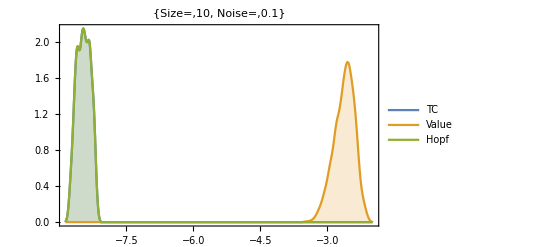
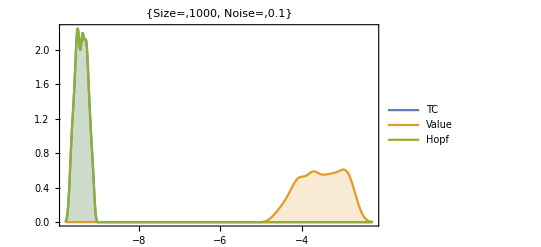
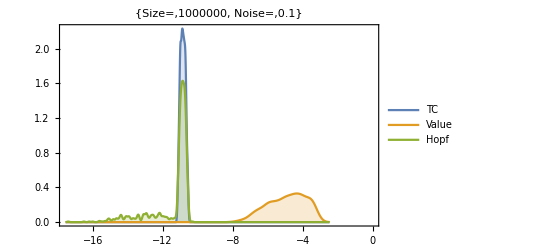
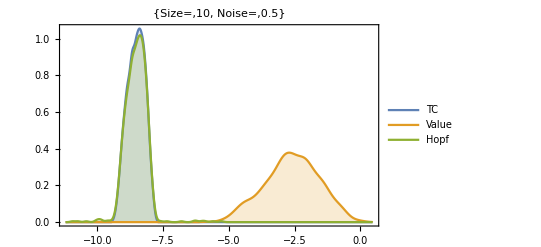
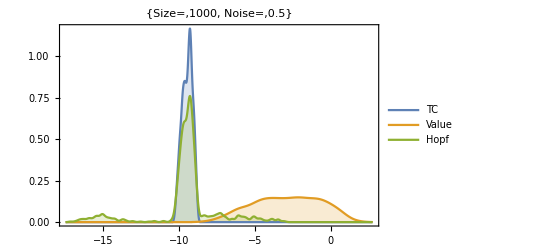
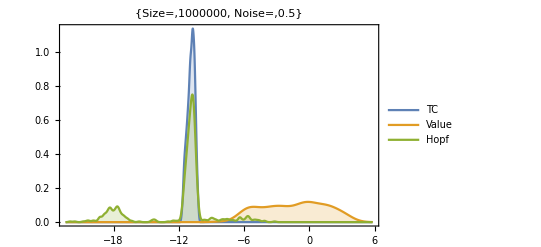

```mathematica
Table[
Table[
SigmaOutput=ParallelTable[
TCMHfunc[
(*ts*)1000,
(*M*)10^(y+RandomReal[{-0.5,0.5}]),
(*B0*)1.9*10^(-2)*(1+RandomReal[{-noise,noise}]),
(*Bm*)0.0245*(1+RandomReal[{-noise,noise}]),
(*Em*)21.39/2*1000(*J/gram*)*(1+RandomReal[{-noise,noise}]),
(*η*)3/4*(1+RandomReal[{-0,0}]),
(*η2*)-0.206*(1+RandomReal[{-0,0}]),
(*λ0*)3.3879*10^(-7)*(1+RandomReal[{-noise,noise}]),
(*ef*)0.01,
(*γ*)1.19*(1+RandomReal[{-noise,noise}]),
(*ζ*)1.01*(1+RandomReal[{-noise,noise}]),
(*f0*)0.0202*(1+RandomReal[{-noise,noise}]),
(*mm0*)0.324*(1+RandomReal[{-noise,noise}])
],{1000}];
SmoothHistogram[{Log[SigmaOutput[[All,1]]],Log[SigmaOutput[[All,2]]],Log[SigmaOutput[[All,3]]]},PlotLegends->{"TC","Value","Hopf"},Filling->Bottom,Frame->True,PlotLabel->{"Size=",10^y,"  Noise=",noise}],
{y,{1,3,6}}],{noise,{0.1,0.5}}]
```

Plotting vital rates as a function of Body Mass

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{growth,starvation,mortality,recovery,maintenance,resourcegrowth}
)
```

```mathematica
Remove[Mass];
RatesByMass =
Table[
parameters={
(*noise*)0.2,
(*ts*)1000,
(*M*)Mass =10^(y+RandomReal[{-0.05,0.05}]),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.000001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324};
R=Ratesfunc[parameters];
{Mass,R},
{y,-2,6,0.01}];
```

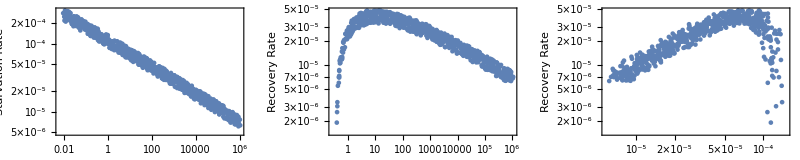

```mathematica
ColorScale = RatesByMass[[All,1]]/Max[RatesByMass[[All,1]]];
RatesPlot=GraphicsGrid[{{
ListLogLogPlot[Transpose[{RatesByMass[[All,1]],RatesByMass[[All,2]][[All,2]]}],Frame->True,FrameLabel->{"Mass","Starvation Rate"}],
ListLogLogPlot[Transpose[{RatesByMass[[All,1]],RatesByMass[[All,2]][[All,4]]}],Frame->True,FrameLabel->{"Mass","Recovery Rate"}],
ListLogLogPlot[Transpose[{RatesByMass[[All,2]][[All,2]],RatesByMass[[All,2]][[All,4]]}],Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]
}},ImageSize->800]
```

```mathematica
parameters={
(*noise*)0,
(*ts*)1000,
(*M*)Mass =10^(y),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.000001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324};
R=Ratesfunc[parameters/.y->2]
```

{0.000131199,0.0461204,0.0046696,0.0347394+0. ⅈ,0.000600833,500.}

```mathematica
Mass
```

10^y

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Rates.pdf",RatesPlot,"PDF",ImageResolution->300]
```

Imaging the Hopf Bifurcation lines

```mathematica
HopfLinefunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
Jac = ({{ts*(λ-(1-R) σ), ts*R ρ, ts*H ρ+F σ}, {ts*(1-R) σ, ts*(-μ-R ρ), ts*(-H ρ-F σ)}, {ts*(-m R), ts*(-R ρ), ts*(-F m+(1-R) α-R α-H ρ)}});
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));

JacSpecSol = FullSimplify[Jac/.{R->Rstar, H->Hstar, F->Fstar}];
(*SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ]*);
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,ρ];


growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]);
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+ RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*0.5*(1 + RandomReal[{-noise,noise}]);
(*Replace everything except rho and sigma to build the curve*)
(*HopfSol = HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth};*)
sigvalues = RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==0.0000001},sig,{n,1,80}];
HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth,σ->sig})]]},{sig,sigvalues}];

out = {growth,HopfSol,starvation,recovery}
)
```

```mathematica
sigvalues = RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==0.0000001},sig,{n,1,80}]
```

{1.×10^-7,1.5×10^-7,2.25×10^-7,3.375×10^-7,5.0625×10^-7,7.59375×10^-7,1.13906×10^-6,1.70859×10^-6,2.56289×10^-6,3.84434×10^-6,5.7665×10^-6,8.64976×10^-6,0.0000129746,0.000019462,0.0000291929,0.0000437894,0.0000656841,0.0000985261,0.000147789,0.000221684,0.000332526,0.000498789,0.000748183,0.00112227,0.00168341,0.00252512,0.00378768,0.00568151,0.00852227,0.0127834,0.0191751,0.0287627,0.043144,0.064716,0.097074,0.145611,0.218416,0.327625,0.491437,0.737155,1.10573,1.6586,2.4879,3.73185,5.59777,8.39666,12.595,18.8925,28.3387,42.5081,63.7622,95.6432,143.465,215.197,322.796,484.194,726.291,1089.44,1634.15,2451.23,3676.85,5515.27,8272.91,12409.4,18614.,27921.1,41881.6,62822.4,94233.6,141350.,212026.,318038.,477057.,715586.,1.07338×10^6,1.61007×10^6,2.4151×10^6,3.62265×10^6,5.43398×10^6,8.15097×10^6}

```mathematica
parameters = {
(*noise*) 0.1,
(*ts*)1000,
(*M*)10^(y+RandomReal[{-0.05,0.05}]),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.000001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324
};
With[{y=1},
Curve = HopfLinefunc[parameters];
Show[{
(*LogLogPlot[Curve[[2]],{σ,0.000001,100},PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]*)

ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,1]]}],PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"},Joined->True],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,2]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,3]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],
(*ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,4]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],*)

Graphics[{Dashed,Line[{{Log@Curve[[1]],Log@0.0000001},{Log@Curve[[1]],1000}}]}],
Graphics[{Red,PointSize[Medium],Point[{Re[Log@Curve[[3]]],Re[Log@Curve[[4]]]}]}]
}]
]
```

$Aborted

With replications

```mathematica
reps = 10;
Remove[y];
Remove[ef];
parameters={
(*noise*) 0.3,
(*ts*)1000,
(*M*)10^(y),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)ef,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324
};

repdataSmall = Table[
HopfLinefunc[parameters/.{ef->0.000001,y->0+RandomReal[{-0.1,0.1}]}],
{reps}];
repdataLargeRich = Table[
HopfLinefunc[parameters/.{ef->0.0001,y->7+RandomReal[{-0.1,0.1}]}],
{reps}];
repdataLargePoor = Table[
HopfLinefunc[parameters/.{ef->0.000001,y->7+RandomReal[{-0.1,0.1}]}],
{reps}];
```

$Aborted

$Aborted

$Aborted

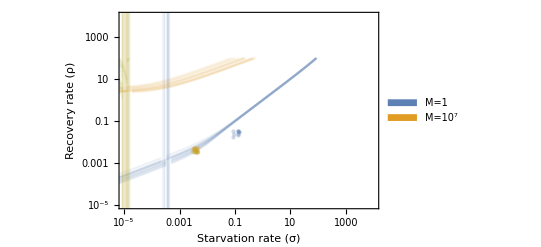

```mathematica
Opac = 0.1;
DataHopfPlot = 
Legended[
Show[
Table[
Show[{
Curve = repdataSmall[[i]];

(*LogLogPlot[Curve[[2]],{σ,0.000001,100},PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]*)

ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,1]]}],PlotRange->{{0.00001,10000},{0.00001,10000}},Frame->True,FrameLabel->{"Starvation rate (σ)","Recovery rate (ρ)"},Joined->True,PlotStyle->Directive[Opacity[Opac]],Axes->False],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,2]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[Opacity[Opac]]],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,3]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[Opacity[Opac]]],
(*ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,4]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],*)

Graphics[{ColorData[97,1],Opacity[Opac],Line[{{Log@Curve[[1]],Log@0.0000001},{Log@Curve[[1]],1000}}]}],
Graphics[{ColorData[97,1],PointSize[Medium],Opacity[Opac+0.2],Point[{Re[Log@Curve[[3]]],Re[Log@Curve[[4]]]}]}]
}],
{i,1,reps,1}],
Table[
Show[{
Curve = repdataLargeRich[[i]];

(*LogLogPlot[Curve[[2]],{σ,0.000001,100},PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]*)

ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,1]]}],PlotRange->{{0.00001,10000},{0.00001,10000}},Frame->True,FrameLabel->{"Starvation rate (σ)","Recovery rate (ρ)"},Joined->True,PlotStyle->Directive[{ColorData[97,3],Opacity[Opac]}],Axes->False],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,2]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[{ColorData[97,3],Opacity[Opac]}]],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,3]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[{ColorData[97,3],Opacity[Opac]}]],
(*ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,4]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],*)

Graphics[{ColorData[97,3],Opacity[Opac],Line[{{Log@Curve[[1]],Log@0.0000001},{Log@Curve[[1]],1000}}]}],
Graphics[{ColorData[97,3],PointSize[Medium],Opacity[Opac+0.2],Point[{Re[Log@Curve[[3]]],Re[Log@Curve[[4]]]}]}]
}],
{i,1,reps,1}],
Table[
Show[{
Curve = repdataLargePoor[[i]];

(*LogLogPlot[Curve[[2]],{σ,0.000001,100},PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]*)

ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,1]]}],PlotRange->{{0.000001,10000},{0.000001,10000}},Frame->True,FrameLabel->{"Starvation rate (σ)","Recovery rate (ρ)"},Joined->True,PlotStyle->Directive[{ColorData[97,2],Opacity[Opac]}]],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,2]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[{ColorData[97,2],Opacity[Opac]}]],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,3]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[{ColorData[97,2],Opacity[Opac]}]],
(*ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,4]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],*)

Graphics[{ColorData[97,2],Opacity[Opac],Line[{{Log@Curve[[1]],Log@0.0000001},{Log@Curve[[1]],1000}}]}],
Graphics[{ColorData[97,2],PointSize[Medium],Opacity[Opac+0.2],Point[{Re[Log@Curve[[3]]],Re[Log@Curve[[4]]]}]}]
}],
{i,1,reps,1}]
],SwatchLegend[{ColorData[97,1],ColorData[97,2]},{"M=1","M=10^7"}]]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_DataHopf.pdf",DataHopfPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_DataHopf.pdf

Plot single parameter values across a range of body sizes

```mathematica
Remove[y];
parameters={
(*noise*) 0,
(*ts*)1000,
(*M*)10^(y),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324
};
massData = Table[
HopfLinefunc[parameters/.y->i],
{i,1,6,0.25}];
```

```mathematica
MassListPlot = Table[
Massexponent = Table[i,{i,1,6,0.25}];
Show[{
Curve = massData[[i]];
Opac=1;
(*LogLogPlot[Curve[[2]],{σ,0.000001,100},PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]*)
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,1]]}],PlotRange->{{0.000001,1000},{0.000001,1000}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"},Joined->True,PlotStyle->Directive[Opacity[Opac]],AxesOrigin->{0,0},PlotLabel->Round[10^Massexponent[[i]],1]],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,2]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[Opacity[Opac]]],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,3]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True,PlotStyle->Directive[Opacity[Opac]]],
(*ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,4]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],*)

Graphics[{ColorData[97,1],Opacity[Opac],Line[{{Log@Curve[[1]],Log@0.0000001},{Log@Curve[[1]],1000}}]}],
Graphics[{ColorData[97,1],PointSize[Medium],Opacity[Opac],Point[{Re[Log@Curve[[3]]],Re[Log@Curve[[4]]]}]}]
}],
{i,1,Length[massData],1}];
```

```mathematica
MassAnimation=ListAnimate[MassListPlot,ControlPlacement->False]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/mov_bodysize.mov",MassAnimation]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/mov_bodysize.mov

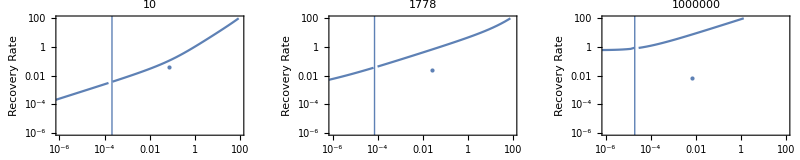

```mathematica
GraphicsGrid[{{MassListPlot[[1]],MassListPlot[[10]],MassListPlot[[21]]}},ImageSize->800]
```

```mathematica
Length[MassListPlot]
```

21

```mathematica
Round[10.3425,1]
```

10

Plotting steady states by rates

```mathematica
SteadyStatesByMass[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
Jac = ({{ts*(λ-(1-R) σ), ts*R ρ, ts*H ρ+F σ}, {ts*(1-R) σ, ts*(-μ-R ρ), ts*(-H ρ-F σ)}, {ts*(-m R), ts*(-R ρ), ts*(-F m+(1-R) α-R α-H ρ)}});
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));

JacSpecSol = FullSimplify[Jac/.{R->Rstar, H->Hstar, F->Fstar}];
(*SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ]*);
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,ρ];


growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]);
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+ RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*1*(1 + RandomReal[{-noise,noise}]);
(*Replace everything except rho and sigma to build the curve*)
(*HopfSol = HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth};*)
sigvalues = RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==0.0000001},sig,{n,1,55}];
HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth,σ->sig})]]},{sig,sigvalues}];

out = {growth,HopfSol,starvation,recovery}
)
```